```mathematica
H1[ν_,F_,t_] := {{-ν/2 t,F},{Conjugate[F],ν/2 t}};
```

```mathematica
lm[ν_,F_,t_]:=Eigenvalues[H1[ν,F,t]][[1]];
```

```mathematica
lp[ν_,F_,t_ ]:= Eigenvalues[H1[ν,F,t]][[2]];
```

```mathematica
Ep[ν_,t_]:= ν/2 t;
```

```mathematica
En[ν_,t_]:= -ν/2 t;
```

```mathematica
Plot1[ν_,F_]:= Plot[{Ep[ν,t],lp[ν,F,t]},{t,0,10},PlotLegends->{"E_+(t,ν="<>ToString[ν]<>")","λ_+(t,ν="<>ToString[ν]<>",F="<>ToLowerCase[ToString[F]]<>")"},
AxesLabel->Automatic]
```

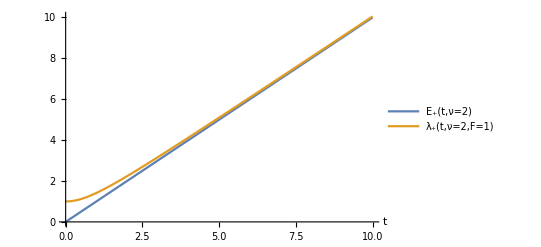

```mathematica
Plot1[2,1]
```